```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
data = Import["phidist.txt","CSV"]
```

{{0,7},{1,5},{2,10},{3,14},{4,19},{5,27},{6,18},{7,33},{8,36},{9,50},{10,26},{11,31},{12,65},{13,59},{14,51},{15,58},{16,51},{17,75},{18,70},{19,68},{20,61},{21,117},{22,70},{23,85},{24,83},{25,88},{26,95},{27,97},{28,92},{29,120},{30,113},{31,132},{32,113},{33,98},{34,134},{35,108},{36,131},{37,134},{38,147},{39,132},{40,144},{41,149},{42,164},{43,180},{44,118},{45,172},{46,183},{47,198},{48,184},{49,153},{50,192},{51,169},{52,195},{53,189},{54,150},{55,194},{56,202},{57,173},{58,214},{59,202},{60,207},{61,189},{62,206},{63,215},{64,212},{65,247},{66,223},{67,231},{68,225},{69,213},{70,231},{71,222},{72,249},{73,232},{74,230},{75,234},{76,235},{77,249},{78,229},{79,261},{80,280},{81,250},{82,237},{83,249},{84,234},{85,266},{86,258},{87,285},{88,259},{89,280},{90,276},{91,292},{92,264},{93,266},{94,310},{95,254},{96,276},{97,304},{98,274},{99,316},{100,253},{101,291},{102,275},{103,284},{104,324},{105,320},{106,333},{107,312},{108,296},{109,296},{110,338},{111,326},{112,291},{113,283},{114,309},{115,331},{116,323},{117,338},{118,300},{119,311},{120,307},{121,312},{122,333},{123,365},{124,320},{125,341},{126,297},{127,322},{128,333},{129,307},{130,349},{131,330},{132,342},{133,371},{134,304},{135,348},{136,327},{137,313},{138,328},{139,333},{140,370},{141,320},{142,361},{143,357},{144,335},{145,356},{146,333},{147,351},{148,364},{149,389},{150,384},{151,331},{152,351},{153,321},{154,367},{155,340},{156,384},{157,359},{158,341},{159,330},{160,377},{161,367},{162,354},{163,311},{164,349},{165,365},{166,401},{167,349},{168,314},{169,342},{170,336},{171,361},{172,326},{173,368},{174,363},{175,375},{176,398},{177,382},{178,364},{179,352},{180,365},{181,388},{182,380},{183,372},{184,353},{185,385},{186,392},{187,387},{188,369},{189,356},{190,413},{191,369},{192,314},{193,374},{194,345},{195,362},{196,365},{197,372},{198,393},{199,327},{200,338},{201,342},{202,345},{203,364},{204,339},{205,359},{206,355},{207,360},{208,369},{209,367},{210,323},{211,347},{212,354},{213,355},{214,368},{215,354},{216,346},{217,358},{218,365},{219,355},{220,336},{221,352},{222,358},{223,314},{224,366},{225,331},{226,346},{227,361},{228,364},{229,352},{230,311},{231,342},{232,352},{233,346},{234,322},{235,321},{236,353},{237,362},{238,341},{239,333},{240,361},{241,335},{242,391},{243,356},{244,317},{245,319},{246,358},{247,333},{248,322},{249,305},{250,341},{251,333},{252,339},{253,350},{254,318},{255,327},{256,327},{257,334},{258,359},{259,305},{260,345},{261,334},{262,322},{263,302},{264,315},{265,302},{266,313},{267,320},{268,315},{269,310},{270,317},{271,297},{272,322},{273,289},{274,281},{275,319},{276,296},{277,328},{278,297},{279,304},{280,326},{281,275},{282,324},{283,290},{284,305},{285,295},{286,258},{287,303},{288,285},{289,294},{290,317},{291,258},{292,272},{293,240},{294,255},{295,284},{296,310},{297,306},{298,269},{299,282},{300,272},{301,261},{302,239},{303,257},{304,282},{305,301},{306,238},{307,262},{308,228},{309,260},{310,229},{311,245},{312,234},{313,242},{314,261},{315,216},{316,257},{317,258},{318,230},{319,242},{320,217},{321,221},{322,237},{323,235},{324,233},{325,220},{326,211},{327,192},{328,243},{329,197},{330,224},{331,194},{332,217},{333,214},{334,173},{335,212},{336,199},{337,200},{338,202},{339,189},{340,202},{341,192},{342,187},{343,176},{344,176},{345,186},{346,154},{347,180},{348,170},{349,164},{350,184},{351,198},{352,187},{353,162},{354,165},{355,164},{356,159},{357,167},{358,150},{359,176},{360,184},{361,183},{362,171},{363,165},{364,142},{365,150},{366,151},{367,150},{368,124},{369,154},{370,144},{371,125},{372,152},{373,153},{374,150},{375,134},{376,125},{377,113},{378,126},{379,126},{380,110},{381,136},{382,151},{383,119},{384,109},{385,121},{386,138},{387,104},{388,142},{389,124},{390,104},{391,99},{392,86},{393,112},{394,95},{395,100},{396,72},{397,103},{398,99},{399,100},{400,99},{401,94},{402,87},{403,93},{404,92},{405,90},{406,96},{407,62},{408,77},{409,76},{410,78},{411,85},{412,101},{413,79},{414,70},{415,77},{416,76},{417,90},{418,70},{419,67},{420,82},{421,59},{422,65},{423,68},{424,70},{425,77},{426,73},{427,55},{428,79},{429,65},{430,52},{431,69},{432,54},{433,52},{434,64},{435,51},{436,59},{437,64},{438,66},{439,51},{440,63},{441,47},{442,48},{443,61},{444,67},{445,48},{446,69},{447,53},{448,49},{449,47},{450,44},{451,60},{452,45},{453,50},{454,47},{455,50},{456,47},{457,45},{458,51},{459,41},{460,38},{461,44},{462,31},{463,46},{464,39},{465,27},{466,28},{467,32},{468,33},{469,18},{470,29},{471,33},{472,38},{473,28},{474,20},{475,29},{476,34},{477,27},{478,26},{479,26},{480,32},{481,24},{482,21},{483,22},{484,25},{485,17},{486,26},{487,26},{488,24},{489,15},{490,21},{491,15},{492,23},{493,21},{494,26},{495,20},{496,17},{497,33},{498,13},{499,15},{500,14},{501,16},{502,8},{503,15},{504,16},{505,11},{506,19},{507,8},{508,16},{509,8},{510,8},{511,11},{512,15},{513,12},{514,6},{515,5},{516,7},{517,9},{518,9},{519,8},{520,9},{521,4},{522,8},{523,9},{524,2},{525,11},{526,9},{527,5},{528,8},{529,5},{530,11},{531,9},{532,3},{533,6},{534,3},{535,7},{536,5},{537,1},{538,1},{539,1},{540,3},{541,1},{542,4},{543,2},{544,3},{545,2},{546,2},{547,2},{548,0},{549,0},{550,0},{551,3},{552,1},{553,0},{554,1},{555,2},{556,1},{557,0},{558,0},{559,0},{560,1},{561,0},{562,0},{563,0},{564,0},{565,1},{566,1},{567,0},{568,0},{569,0},{570,0},{571,0},{572,0},{573,0},{574,0},{575,0},{576,0},{577,0},{578,0},{579,0},{580,0},{581,0},{582,0},{583,0},{584,0},{585,0},{586,0},{587,0},{588,0},{589,0},{590,0},{591,0},{592,0},{593,0},{594,0},{595,0},{596,0},{597,0},{598,0},{599,0},{600,0},{601,0},{602,0},{603,0},{604,0},{605,0},{606,0},{607,0},{608,0},{609,0},{610,0},{611,0},{612,0},{613,0},{614,0},{615,0},{616,0},{617,0},{618,0},{619,0},{620,0},{621,0},{622,0},{623,0},{624,0},{625,0},{626,0},{627,0},{628,0},{629,0},{630,0},{631,0},{632,0},{633,0},{634,0},{635,0},{636,0},{637,0},{638,0},{639,0},{640,0},{641,0},{642,0},{643,0},{644,0},{645,0},{646,0},{647,0},{648,0},{649,0},{650,0},{651,0},{652,0},{653,0},{654,0},{655,0},{656,0},{657,0},{658,0},{659,0},{660,0},{661,0},{662,0},{663,0},{664,0},{665,0},{666,0},{667,0},{668,0},{669,0},{670,0},{671,0},{672,0},{673,0},{674,0},{675,0},{676,0},{677,0},{678,0},{679,0},{680,0},{681,0},{682,0},{683,0},{684,0},{685,0},{686,0},{687,0},{688,0},{689,0},{690,0},{691,0},{692,0},{693,0},{694,0},{695,0},{696,0},{697,0},{698,0},{699,0},{700,0},{701,0},{702,0},{703,0},{704,0},{705,0},{706,0},{707,0},{708,0},{709,0},{710,0},{711,0},{712,0},{713,0},{714,0},{715,0},{716,0},{717,0},{718,0},{719,0},{720,0},{721,0},{722,0},{723,0},{724,0},{725,0},{726,0},{727,0},{728,0},{729,0},{730,0},{731,0},{732,0},{733,0},{734,0},{735,0},{736,0},{737,0},{738,0},{739,0},{740,0},{741,0},{742,0},{743,0},{744,0},{745,0},{746,0},{747,0},{748,0},{749,0},{750,0},{751,0},{752,0},{753,0},{754,0},{755,0},{756,0},{757,0},{758,0},{759,0},{760,0},{761,0},{762,0},{763,0},{764,0},{765,0},{766,0},{767,0},{768,0},{769,0},{770,0},{771,0},{772,0},{773,0},{774,0},{775,0},{776,0},{777,0},{778,0},{779,0},{780,0},{781,0},{782,0},{783,0},{784,0},{785,0},{786,0},{787,0},{788,0},{789,0},{790,0},{791,0},{792,0},{793,0},{794,0},{795,0},{796,0},{797,0},{798,0},{799,0},{800,0},{801,0},{802,0},{803,0},{804,0},{805,0},{806,0},{807,0},{808,0},{809,0},{810,0},{811,0},{812,0},{813,0},{814,0},{815,0},{816,0},{817,0},{818,0},{819,0},{820,0},{821,0},{822,0},{823,0},{824,0},{825,0},{826,0},{827,0},{828,0},{829,0},{830,0},{831,0},{832,0},{833,0},{834,0},{835,0},{836,0},{837,0},{838,0},{839,0},{840,0},{841,0},{842,0},{843,0},{844,0},{845,0},{846,0},{847,0},{848,0},{849,0},{850,0},{851,0},{852,0},{853,0},{854,0},{855,0},{856,0},{857,0},{858,0},{859,0},{860,0},{861,0},{862,0},{863,0},{864,0},{865,0},{866,0},{867,0},{868,0},{869,0},{870,0},{871,0},{872,0},{873,0},{874,0},{875,0},{876,0},{877,0},{878,0},{879,0},{880,0},{881,0},{882,0},{883,0},{884,0},{885,0},{886,0},{887,0},{888,0},{889,0},{890,0},{891,0},{892,0},{893,0},{894,0},{895,0},{896,0},{897,0},{898,0},{899,0},{900,0}}

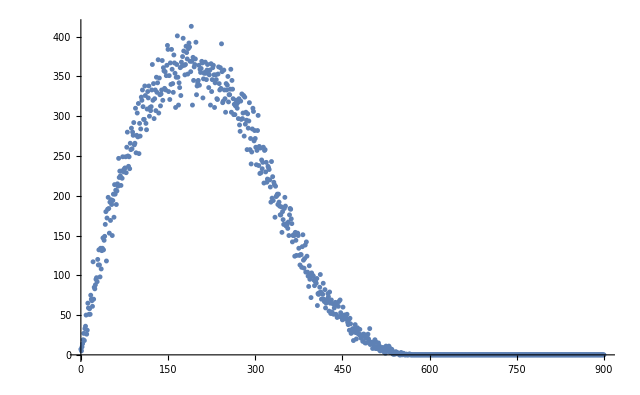

```mathematica
ListPlot[data]
```

```mathematica
data2 = Import["new.txt","CSV"]
```

{{109,273},{109,277},{109,278},{109,339},{109,340},{109,341},{109,342},{109,344},{109,345},{109,346},{109,353},{109,354},{109,355},86459,{493,374},{494,269},{494,271},{494,272},{494,283},{494,284},{494,285},{494,327},{494,360},{494,361},{494,362},{495,361}}
 |  |  |  |

```mathematica
data3 = Import["type2.txt","CSV"]
```

{{110,300},{110,313},{110,331},{110,332},{111,300},{111,301},{111,313},{111,331},{112,264},{112,284},{112,285},{112,286},{112,300},79209,{494,318},{494,319},{494,320},{494,336},{494,342},{494,354},{494,356},{495,314},{495,315},{495,316},{495,319},{495,320}}
 |  |  |  |

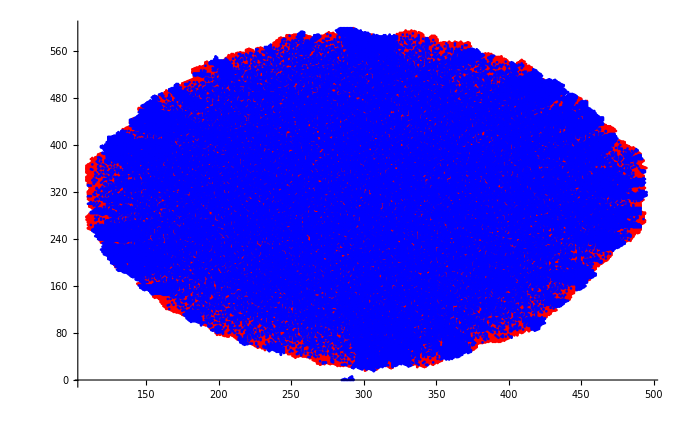

```mathematica
ListPlot[{data2,data3},PlotStyle->{Red,Blue}]
```